# Build a Hopper Simulation

Wei-Hsi Chen

Pre: understanding of EOM

## 1.1 Bouncing Ball (simplify mechanics)

Quiz: the equation of motion for a mass-spring-damper system; a fallen apple (ballistic)

Let us start with a very simple bouncing ball problem. We want to see how many bounce an elastic ball makes until it stops when it falls freely from a given height. We know that the ball have a ballistics behavior in its flight phase; the compressing and releasing phase on ground behaves like a mass-spring-damper system. Recall that if we don’t have a damper in our system, we won’t see any decrement in energy and the ball will bounce forever. Typically this is not an easy problem, by this I mean we cannot solve it analytically and there is no closed form solution.

We release an elastic ball with radius r=0.05m and mass m=1kg from a height h=1m, and the total energy of the ball at this initial point is E. Let’s start by simplifying the problem, we will make a naive assumption that the ground consume a certain portion of energy every time the ball crashes the ground, returning only a portion of γ=0.5 of the previous energy. We also assume the collision happens at an instance and doesn’t take any time at all, thus the deformation during that time is neglected.

Write down the initial energy of the system E, then find the ratio of the velocity before and after the collision.

```mathematica
E== 1/2 m y'[t]^2+m g h[t]
Subscript[E, 2]==γ Subscript[E, 1]-> Subscript[v, 2]^2==γ Subscript[v, 1]^2-> Subscript[v, 2]/Subscript[v, 1]=-√γ
```

Now construct our equation of motion as a initial value problem with a set of first order ODEs having different assigned velocity after every collision

```mathematica
Piecewise[{{y'[t]=v[t], }, {v'[t]=-g, }}],y[0]= h, v[0]=0, v[t]=-√γ v[t-1] when collision
```

Using ODE45 (MatLab) or NDSolve (Mathematica), solve the equation of motion numerically or analytically  and plot the solution with respect to time. End the solver after the apec of the ball goes lower than hs=0.055m.

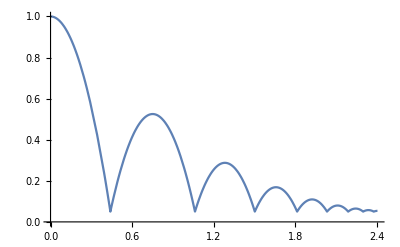

```mathematica
ball=NDSolve[{y''[t]==-9.81,y[0]==1,y'[0]==0,WhenEvent[y[t]==0.05,y'[t]->-√0.5 y'[t]],WhenEvent[y'[t]==0 && y[t]≤0.055,end=t;"StopIntegration"]},y,{t,0,20}];
Plot[y[t]/.ball,{t,0,end}]
```

## 1.2 Bouncing Ball (MSD system)

Now let’s revisit the bouncing ball problem in a more sophisticated matter. Remember that our ball have a ballistics behavior (1) in its flight phase and behaves like a mass-spring-damper system (2) on the stance phase. Rewrite the equation of motion given from (1) and (2) into a dynamic system state space representation Ẏ=f(Y) (first order ODEs) with initial values and carefully states the events.

```mathematica
(1) m y''[t]==-m g 
(2) m y''[t]+b y'[t]+k y[t]==-m g
```

```mathematica
Piecewise[{{y'[t]=v[t], }, {v'[t]=-g, }}],flight
Piecewise[{{y'[t]=v[t], }, {v'[t]=-b/m v[t] -k/m (y[t]-restlength)-g, }}],stance, when y[t]≤stance length
y[0]= h,v[0]=0
```

The equation of motion looks more complicated now since this is a finite-state mechanism. Now solve the equation of motion numerically or analytically and plot the solution with respect to time. Again, end the solver after the apec of the ball goes lower than hs=0.055m.

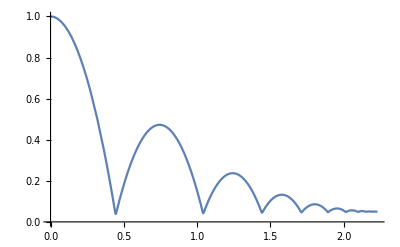

```mathematica
ClearAll;Clear[end];
restLength  = 0.05;
b = 80;
k = 100000;
msdball=NDSolve[{ y''[t]+stance[t](b y'[t]+k( y[t]-restLength))==-9.81,y[0]==1,y'[0]==0,stance[0]==0,
WhenEvent[y[t]≤restLength,{stance[t]->1}],
WhenEvent[y[t]>restLength,{stance[t]->0}],
WhenEvent[y'[t]==0 && 0.055≥y[t]>restLength,end=t]},
{y,stance},{t,0,10},DiscreteVariables->{stance}];
Plot[Evaluate[{y[t]}/.msdball],{t,0,end}]
```

## 1.3 Paddling (Joggling) (model, stability proof)

We have now found out the motion of a bouncing ball when it is let loose from a given height. Due to the damper consuming energy in the system, the ball will eventually stop bouncing. Thus if we want to make the ball bounce forever, we could inject some energy into the system to compensate those that are consumed from the damper.

Imagine you are paddling the elastic ball upward with a flat solid paddle. Supposed that you are a professional and you manage to have the ball touch down at the same position, and once center of mass of the ball is at its exact lowest point, you provide a constant uniform force throughout the rest of the collision until the ball takes off at the same height it touches down every time. Since we are now actively providing energy into the system, i.e., the work done by the force transmitted to the ball via the paddle, we can imagine that the ball will eventually bounce at a constant height, and it would go on forever if we provide the energy it needs nonstop.

Rewrite the Equation of motion into a forced dynamic system in the form of Ẏ=f(Y)+g(u), where g(u) is the control law of this problem. The control law u(t) we have is a uniform constant force τ that is applied throughout the stance phase, that is, u(t)=τ. Again, carefully states the conditions with the initial conditions.

```mathematica
Piecewise[{{y'[t]=v[t], }, {v'[t]=-g, }}],flight
Piecewise[{{y'[t]=v[t], }, {v'[t]=-b/m v[t] -k/m (y[t]-restlength)-g+u[t], }}],stance, when y[t]≤stance length
y[0]= h,v[0]=0,u[t]=τ
```

Now solve the equation of motion numerically or analytically and plot the solution with respect to time assuming that τ=500 for a sufficient time. Can you see that the ball is graduality bouncing toward a certain height? How high is it?

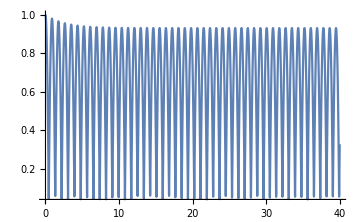

```mathematica
ClearAll[b,k,c];
tdLength  = 0.05;
b = 80;
k = 100000;
msdball=NDSolve[{ y''[t]+stance[t](b y'[t]+k( y[t]-tdLength)-c[t])==-9.81,y[0]==1,y'[0]==0,stance[0]==0,c[0]==0,
WhenEvent[y[t]≤tdLength,{stance[t]->1}],
WhenEvent[y'[t]≥0,c[t]-> 500],
WhenEvent[y[t]>tdLength,{stance[t]->0,c[t]->0}]},
y,{t,0,40},DiscreteVariables->{stance,c}];
Plot[{y[t]}/.msdball,{t,0,40},PlotRange->Full]
```

(Extra; might be too hard) If we want the ball to constantly bounce toward a certain height, can you predict what τ should be?
h=1.5, h=2?

## 1.4 POGO stick (active hopper)

From now on we will leave the bouncing ball with a paddle problem and to look at a POGO stick. Surprisingly, the equation of motions that describe the two system are still the same. The main difference between the bouncing ball with a paddle problem and the pogo stick problem is that we will inject the energy through an actuator attached on the system, whereas the energy was injected through the ground then to the system. To Jump on a Pogo stick, players could use their leg muscles to generate or dissipate energy by bending their knees. Exercising muscle is the most common actuator in living being, whereas in the artificial world, actuators could be motors, linear actuators, pneumatic actuators etc.

Two common way to assemble a Pogo stick uses a linear (cord) spring or a pneumatic spring. Pneumatic spring usually can provide more force to the system than the linear spring and is often used in higher loading task, whereas linear spring is more sensitive (higher bandwidth) and is generally used for more agile task. Due to the different mechanism, the controlling strategies are quite different as well. Here we will simulate a few actuator model for our control input u(t) for the few different mechanism.

#### Linear spring with linear actuator

One of the two common Pogo sticks uses linear spring. Assume that In addition to the original mass-spring-damper system, we have a linear actuator attached and in parallel to the spring-damper. This theoretical linear actuator is weightless and generate torques as desired. Assume that the liner actuator provides a constant force τ throughout the stance phase, it follows that our control law looks exactly like the ball-paddling problem, u(t)=τ. And the simulation shows the same results.

#### Pneumatic actuator

Another common Pogo sticks is assembled with a pneumatic spring. A pneumatic spring gains its springiness by compressing either air or other fluids. Assume that the filling gas in the pneumatic spring is ideal and the temperature does not change during the compression, then according to Boyle’s law, the product of the pressure and the volume is constant, that is, p V=C_1. Find out the air spring force law F_pneu=f(x,V, A, p, C_1) that the pneumatic spring gives given the notations from Figure?.

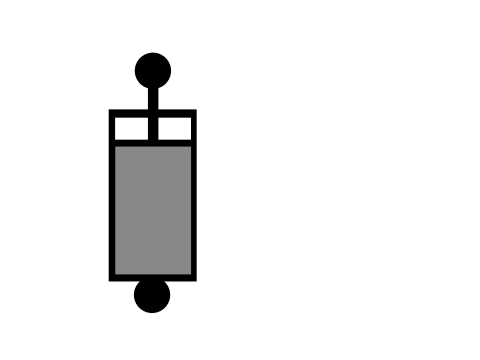

```mathematica
p V=C1; F/A x A =F x=C1; F=C1/x
```

Assume that we change the stiffness of the spring at the lowest point of the stance phase by injecting gas into the air chamber, the air would press the spring back up, leading the Pogo stick to jump up. Assume we inject gas into the chamber such that the molecules are multiply N times from the lowest points to the take off points, with the ideal gas law (p V=n R T), write down the additional force produced by our action in terms of F_add=f(Y,V, A, p, C_1, N). We will set our control law to be u=F_add  from the lowest points to the take off points of the stance phase. The imperial system does not behave like a ideal gas and there are heat loss during the compression, for a simplify version, we say that the heat loss also takes the terms same as the damper, that is, b Ẏ. Again, write down the Equation of motion for the controlled system Ẏ=f(Y)+g(u).

```mathematica
Piecewise[{{y'[t]=v[t], }, {v'[t]=-g, }}],flight
Piecewise[{{y'[t]=v[t], }, {v'[t]=-b/m v[t] +C1/m (1/y[t])-g+u[t], }}],stance, when y[t]≤stance length
y[0]= h,v[0]=0,u[t]=Piecewise[{{0, v[t]<0}, {((N-1) C1)/m (1/y[t]), v[t]>0}}]
```

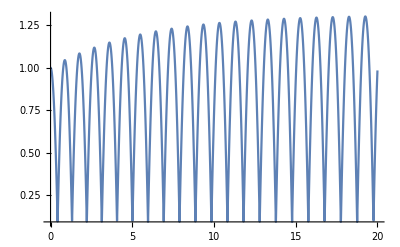

```mathematica
ClearAll;
tdLength  = 0.1;
b = 80;
pneuPogo=NDSolve[{ y''[t]+stance[t](b y'[t]-C1[t]( 1/y[t]))==-9.81,y[0]==1,y'[0]==0,stance[0]==0,C1[0]==100,
WhenEvent[y[t]≤tdLength,stance[t]->1],
WhenEvent[y'[t]≥0,C1[t]->150],
WhenEvent[y[t]>tdLength,{stance[t]->0,C1[t]->100}]},
{y,stance,C1},{t,0,20},DiscreteVariables->{stance,C1}];
Plot[Evaluate[{y[t]}/.pneuPogo],{t,0,20},PlotRange->Full]
```

#### Electromagnetic Virtual Spring (Stiffness Modulation)

From the previous Pneumatic model we can see how convenient it would be to have a hopper with a controllable stiffness. The dynamic of the system can be easily represented as Ẏ=f(Y,N). In real world, the implementation of a pneumatic spring is made hard due to the fact that a pneumatic pump is heavy and bulky. Assume there is a way we could control the stiffness of a Hooke-law spring; in fact, assume that we can construct a virtual Hooke-law spring via an electromagnetic actuator, then by manipulating the spring constant, we should be able to control the hopper to jump.

The full control scheme will now be: assume that we have a stiffness-adjustable Hooke-law spring with a general spring constant of k. Every time the hopper reaches its bottom point, we will change the spring constant into N k, due to Hooke’s law, the spring should press up with a spring-loaded force. Assume that we have a general damping term b Y, then the system would balance eventually. Write down the Equation of motion for the Electromagnetic Virtual Spring system.

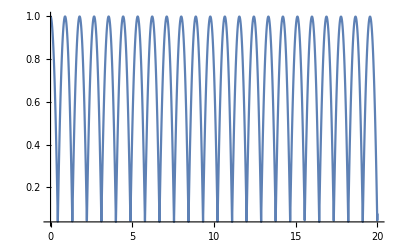

```mathematica
ClearAll;
tdLength  = 0.05;
b = 80;
elecPogo=NDSolve[{ y''[t]+stance[t](b y'[t]+k[t]( y[t]-tdLength))==-9.81,y[0]==1,y'[0]==0,stance[0]==0,k[0]==100000,
WhenEvent[y[t]≤tdLength,stance[t]->1],
WhenEvent[y'[t]≥0,k[t]->194950],
WhenEvent[y[t]>tdLength,{stance[t]->0,k[t]->100000}]},
{y,stance,k},{t,0,40},DiscreteVariables->{stance,k}];
Plot[Evaluate[{y[t]}/.elecPogo],{t,0,20},PlotRange->Full]
```

#### Electromagnetic Virtual Spring (Active Damping)

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

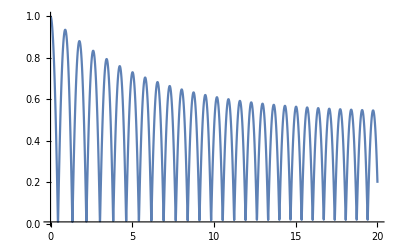

```mathematica
ClearAll;
tdLength  = 0.05;
ω = 100;
β=0.04;
kt=25;
elecPogo=NDSolve[{ y''[t]+stance[t](2ω β y'[t]+ ω^2( y[t]-tdLength)-c[t])==-9.81,
c[t]==(kt y'[t])/(√((ω ( y[t]-tdLength))^2+(y'[t])^2)),y[0]==1,y'[0]==0,stance[0]==0,
WhenEvent[y[t]≤tdLength,stance[t]->1],
(*WhenEvent[y'[t]≥0,k[t]->194950],*)
WhenEvent[y[t]>tdLength,stance[t]->0]},
{y,stance},{t,0,40},DiscreteVariables->{stance}];
Plot[Evaluate[{y[t]}/.elecPogo],{t,0,20},PlotRange->Full]
```

## 1.5 Five-bar-linkage Legs

Until now, we have been looking at a very simple version of a hopper. This simple mass-spring-damper model is what we call a “template” of a hopper. A template is the simplest model that exhibits a targeted behavior [template paper]. We can now try to embed more joints and actuator into the system, like what a leg really could look like, and this action is called anchoring. The reason for anchoring could be that we want to add more actuator to strengthen the system or to make a system more realisable. In the case of the Electromagnetic virtual spring model hopper mentioned in last chapter is hard to realise do to the fact that linear actuator is slow and bulky, thus we will anchor this design to a more applicable mechanism.

We have introduce the Minitaur leg (five-bar linkage) in the class, this is a good example of anchoring a simple hopper template into a more sophisticated mechanism. The two motors provides two degree of freedom for this mechanism, in the radial direction and axial direction. Try to find the kinematic mapping f:(θ1,θ2)→(r,θ) between the angle of two motors to the radial direction and axial direction given Figure ?.

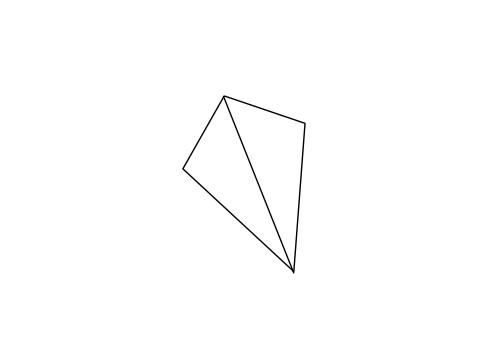

```mathematica
FullSimplify[Solve[l2^2==l1^2+r^2-2 l1 r Cos[α],r]/.α->(2π-(θ1+θ2))/2]
```

{{r→-l1 Cos[(θ1+θ2)/2]-√(-l1^2/2+l2^2+1/2 l1^2 Cos[θ1+θ2])},{r→-l1 Cos[(θ1+θ2)/2]+√(-l1^2/2+l2^2+1/2 l1^2 Cos[θ1+θ2])}}

```mathematica
({{r}, {θ}})==({{-l1 Cos[(θ1+θ2)/2]+√(-l1^2/2+l2^2+1/2 l1^2 Cos[θ1+θ2])}, {(2π+θ1-θ2)/2}})
```

To anchor our simple hopper template into the Minitaur leg, we will have to find the inverse kinematic of the system. We want to represent our two motor control input in terms of the radius and the angle of the simple hopper, i.e., g:(r,θ)→(θ1,θ2) . Find the inverse kinematic of the system.

```mathematica
Solve[{l2^2==l1^2+r^2-2 l1 r Cos[(2π-(θ1+θ2))/2],θ==(2π+θ1-θ2)/2},{θ1,θ2}]/.C[1]->0
```

{{θ1→θ-ArcCos[(l1^2-l2^2+r^2)/(2 l1 r)],θ2→2 π-θ-ArcCos[(l1^2-l2^2+r^2)/(2 l1 r)]},{θ1→θ+ArcCos[(l1^2-l2^2+r^2)/(2 l1 r)],θ2→2 π-θ+ArcCos[(l1^2-l2^2+r^2)/(2 l1 r)]}}

Let us now focus on the vertical hopping and neglect the radial movement, assume that the two motor is symmetric, i.e. θ1==θ2==ξ, we can then control the length of the hopper with a rotation input ξ. Again, write down the kinematic mapping f:ξ→r and the inverse kinematic mapping g:r→ξ.

```mathematica
r==-l1 Cos[ξ]+√(-l1^2/2+l2^2+1/2 l1^2 Cos[2ξ])
```

```mathematica
Solve[l2^2==l1^2+r^2-2 l1 r Cos[π-ξ],ξ]/.C[1]->0
```

{{ξ→-ArcCos[(-l1^2+l2^2-r^2)/(2 l1 r)]},{ξ→ArcCos[(-l1^2+l2^2-r^2)/(2 l1 r)]}}

Now anchor the Electromagnetic virtual spring model onto the Minitaur leg model by finding what the control input should be using our inverse kinematic mapping.

```mathematica
(-0.03^2+0.05^2-y[t]^2)/(2 0.03y[t])/.y[t]->0.05
ArcCos[(-0.025^2+0.05^2-y[t]^2)/(2 0.025y[t])]/.y[t]->0.05
```

-0.3

1.82348

```mathematica
ArcCos[0]
```

π/2

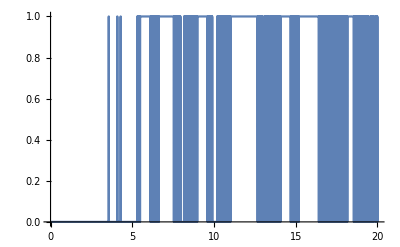

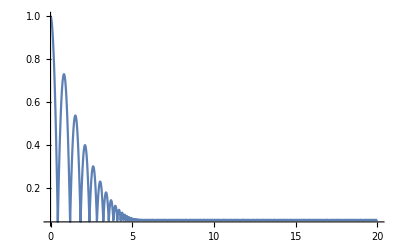

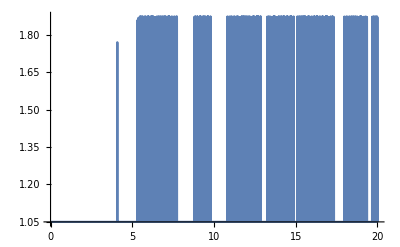

```mathematica
ClearAll;
tdLength  = 0.05;
b = 120;
elecPogo=NDSolve[{ y''[t]+stance[t](b y'[t]+k[t]( y[t]-tdLength))==-9.81,y[0]==1,y'[0]==0,stance[0]==0,k[0]==100000,
WhenEvent[y[t]≤tdLength,stance[t]->1],
WhenEvent[y'[t]≥0,k[t]->194950],
WhenEvent[y[t]>tdLength,{stance[t]->0,k[t]->100000}]},
{y,stance,k},{t,0,40},DiscreteVariables->{stance,k}];
Plot[Evaluate[Boole[y[t]<=0.05/.elecPogo]],{t,0,20},PlotRange->Full]
Plot[Evaluate[y[t]/.elecPogo],{t,0,20},PlotRange->Full]
Plot[Evaluate[{Boole[y[t]<=0.05]ArcCos[(-0.025^2+0.05^2-y[t]^2)/(2 0.025y[t])]+Boole[y[t]>0.05]+tdLength}/.elecPogo],{t,0,20},PlotRange->Full]
```

```mathematica
L=1/2*m*x'[t]^2+1/2*k*(x[t]-l)^2;
D[D[L,x'[t]],t]-D[L,x[t]]==0
```

-k (-l+x[t])+m x''[t]==0